```mathematica
repRate=100(*RF repetition rate*);
(*minPulses=5000 (*minimum number of pulses at a power before increasing? might not need this*);*)
increaseRate=10000/30000 (*rate aim in W per pulse*);
```

```mathematica
time[pulse_]:=pulse/repRate (*time in seconds at pulse number*);
timeIncreaseRate=10000./time[30000] (*rate aim in W per second*)
```

33.3333

```mathematica
aim=10^7;
pulseAim=aim/increaseRate;
timeAim=aim/timeIncreaseRate
```

300000.

```mathematica
shortTimeAim=aim*0.2/timeIncreaseRate
```

60000.

```mathematica
timeAim+7*shortTimeAim
```

720000.

```mathematica
720000./3600
```

200.

```mathematica
Clear[powerIncrease]
normalPowerIncrease=10000(*the normal amount to increase the power*);
linearIncreaseRateLimit=1000000 (*go up to this power (in W)in linear steps*);
powerIncrease[pulse_]:=Ceiling[Piecewise[{{pulse/(linearIncreaseRateLimit/(increaseRate*normalPowerIncrease)),pulse<linearIncreaseRateLimit/increaseRate}},normalPowerIncrease],1000](*Power increase step or function*);
```

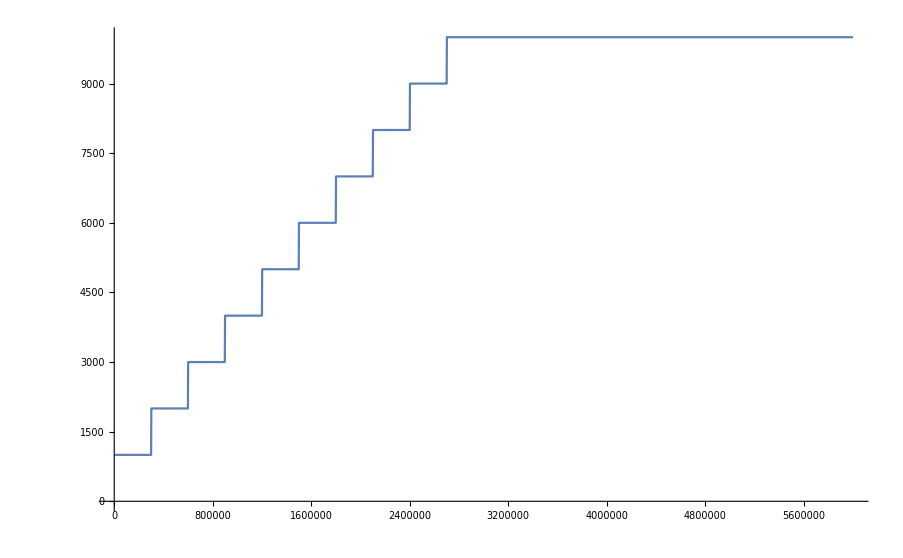

```mathematica
Plot[powerIncrease[x], {x,0,6000000}]
```

```mathematica
Clear[ power]
power[pulse_]:=Ceiling[pulse*increaseRate,powerIncrease[pulse]]
```

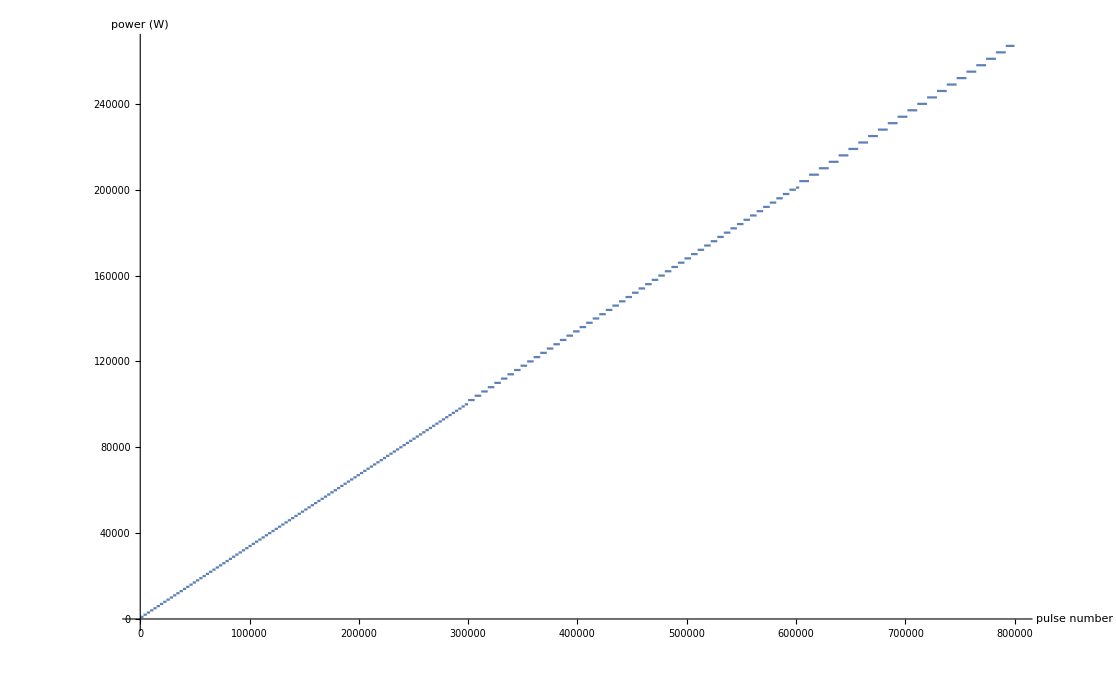

```mathematica
Plot[power[x], {x,0,800000}, PlotPoints->20000, MaxRecursion->2, AxesLabel->{"pulse number","power (W)"}]
```

```mathematica
timepower[time_]:=Ceiling[time*timeIncreaseRate,powerIncrease[time*repRate]]
```

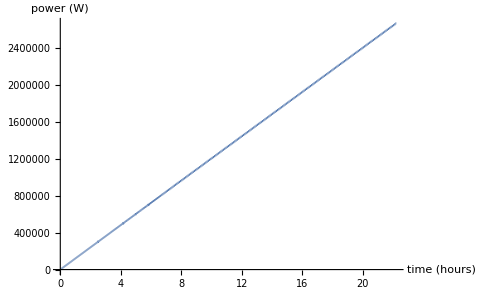

```mathematica
Plot[timepower[3600x], {x,time[0000000]/3600,time[8000000]/3600}, PlotPoints->40000, MaxRecursion->3,AxesLabel->{"time (hours)","power (W)"}]
```

```mathematica
timepowerpiecewise[time_?NumericQ]:=Piecewise[{{timepower[time],time<timeAim},{timepower[time-shortTimeAim], timeAim<time<timeAim+shortTimeAim},{timepower[time-2*shortTimeAim], timeAim+shortTimeAim<time<timeAim+2*shortTimeAim},{timepower[time-3*shortTimeAim], timeAim+2*shortTimeAim<time<timeAim+3*shortTimeAim},{timepower[time-4*shortTimeAim], timeAim+3*shortTimeAim<time<timeAim+4*shortTimeAim},{timepower[time-5*shortTimeAim], timeAim+4*shortTimeAim<time<timeAim+5*shortTimeAim},{timepower[time-6*shortTimeAim], timeAim+5*shortTimeAim<time<timeAim+6*shortTimeAim},{timepower[time-7*shortTimeAim], timeAim+6*shortTimeAim<time<timeAim+7*shortTimeAim}}]
```

```mathematica
timeAim*0.2*8+timeAim
```

780000.

```mathematica
780000./3600
```

216.667

```mathematica
216.66666666666666/12
```

18.0556

```mathematica
timeAim
```

300000.

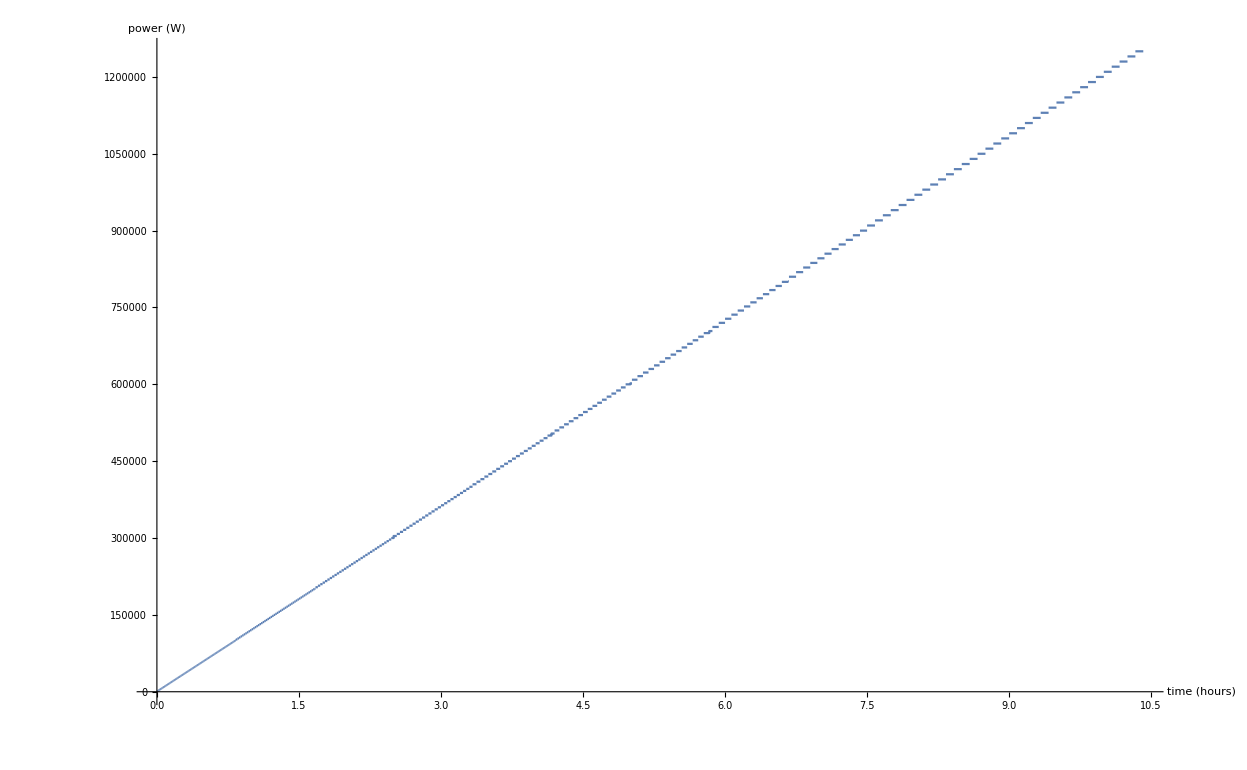

```mathematica
Quiet[Plot[timepowerpiecewise[3600 x], {x,time[0]/3600,(timeAim/8)/3600}, PlotPoints->40000, MaxRecursion->3,AxesLabel->{"time (hours)","power (W)"}]]
```

```mathematica
200/12.
```

16.6667

```mathematica
Clear[eField]
```

```mathematica
eField[x_]:=Sqrt[0.6 timepowerpiecewise[x]]/2449.489742783178*100
```

```mathematica
Table[eField[3600 x],{x,(timeAim-0.01*shortTimeAim)/3600,(timeAim+0.01*shortTimeAim)/3600,0.01}]
```

{99.8999,99.95,99.95,99.95,99.95,99.95,99.95,99.95,99.95,100.,100.,100.,100.,100.,100.,100.,100.,89.4986,89.4986,89.4986,89.4986,89.4986,89.4986,89.4986,89.4986,89.5545,89.5545,89.5545,89.5545,89.5545,89.5545,89.5545,89.5545,89.5545}

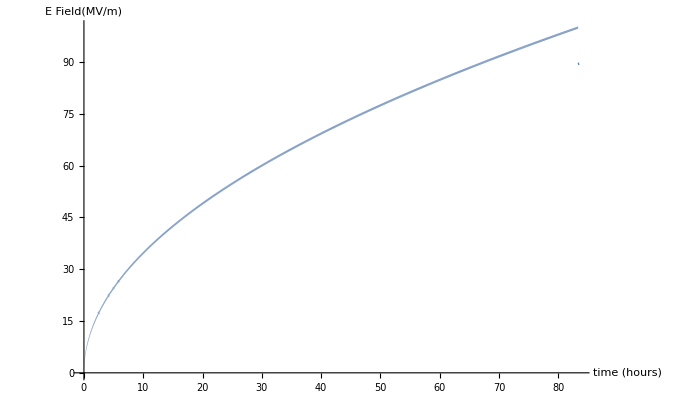

```mathematica
Plot[eField[3600 x], {x,time[0]/3600,(timeAim+0.01*shortTimeAim)/3600}, PlotPoints->40000, MaxRecursion->3,AxesLabel->{"time (hours)","E Field(MV/m)"}]
```

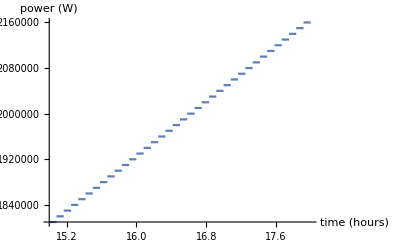

```mathematica
Plot[timepowerpiecewise[3600 x], {x,15,18}, PlotPoints->10000, MaxRecursion->5,AxesLabel->{"time (hours)","power (W)"}]
```

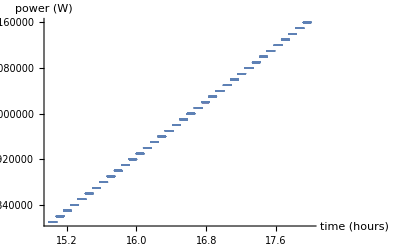

```mathematica
ListPlot[Transpose[{Range[15,18,.0001],timepowerpiecewise[3600 #]&/@Range[15,18,.0001]}],AxesLabel->{"time (hours)","power (W)"}]
```